## Initialization

```mathematica
On[Assert];
```

### Positions of the fields of Model Parameters data structure

```mathematica
fN=1; (*Population Size*)
fO=2;(*Number of owners*)
fW=3;(*Number of workers*)
fSo=4;(*Number of owners in selectorate*)
fSw=5;(*Number of workers in selectorate*)
fWCo=6;(*Number of owners in winning coalition*)
fWCw=7;(*Number of workers in winning coalition*)
fδ=8;(*Continuation value*)
fProductivity=9;(*Total productivity*)
fSalaryO=10;(*Owner Salary*)
fSalaryW=11;(*Worker Salary*)
fCo=12;(*productivity-per-capita units given to each owner*)
fCw=13;(*productivity-per-capita units given to each worker*)
fS=14;(*Total selectorate size*)
fP=15;(*Cost of public goods*)
fWC=16;(*Total Winning Coalition size*)
fParameterFieldCount=16;
```

### Positions of the fields of Strategy data structures

A strategy data-structure can be either for a simple game or for a WO-game. A simple game strategy holds four fields: the payoff, tax-rate, public-goods and private-goods. A WO-game strategy holds two simple-game strategies, for two different sets of model parameters.

```mathematica
fValue=1;(*Holds the payoff of the strategy*)
fR=2;(*Tax rate of the strategy*)
fX=3;(*Ammount of public goods*)
fG=4;(*Ammount of private goods*)
fOpenParameters=7;(*Contains the parameters for the "open borders" scenario*)
fClosedParameters=8;(*Contains the parameters for the "closed borders" scenario*)
fOpenStrategy=5; (*Contains the best simple strategy for the "open borders" scenario*)
fClosedStrategy=6;(*Contains the best simple strategy for the "closed borders" scenario*)
fOpen=9;(*A Boolean indicating whether the open strategy has higher payoff than the closed strategy*)
fWinningStrategy=10; (*The strategy (open or closed) with higher payoff*)
fLosingStrategy=11; (*The strategy (open or closed) with lower payoff*)
fWinningParameters=12; (*The parameters (open or closed) for which the corresponding strategy has higher payoff*)
fLosingParameters=13;(*The parameters (open or closed) for which the corresponding strategy has lower payoff*)
fStrategyFieldCount=4;
fWOStrategyFieldCount=13;
```

### Initialization of Model Parameters data structure

`CheckParameters` verifies if the given parameters are within the correct range.

```mathematica
CheckParameters[p_]:=
Block[{},
Assert[p⟦fN⟧ ≥ 1];
(*Assert[1≤p⟦fWC⟧ ≤p⟦fS⟧/2-1];*)
Assert[1≤p⟦fWC⟧ ≤p⟦fS⟧];
Assert[1≤p⟦fS⟧ ≤p⟦fN⟧];
Assert[0.0≤p⟦fδ⟧ ≤1.0];
Assert[p⟦fO⟧ ≥ 1];
Assert[p⟦fW⟧ ≥ 1];
Assert[p⟦fSo⟧ ≥ 1];
Assert[p⟦fSw⟧ ≥ 1];
Assert[p⟦fProductivity⟧ ≥ 1];
Assert[p⟦fCo⟧×p⟦fO⟧ < p⟦fN⟧];

];
```

`Parameters` initializes a new instance containing all the parameters of the model.

“O ∈ N” - the number of Owners

“W ∈ N” - the number of Workers

“S ∈ N” - the size of the selectorate

“P ∈ N” - the price of public goods

“WCo ∈ N” - the number of owners in the winning coalition

“WCw ∈ N” - the number of workers in the winning coalition

“δ”  ∈ [0, 1] - the continuation value

“Productivity ∈ N” - the ammount of goods produced

“Co” - the number of productivity per capita units (Productivity/(O + W)) that each owner gets. The remaining productivity is equally divided among workers.

```mathematica
Parameters[O_, W_, S_, P_, WCo_, WCw_, δ_, Productivity_, Co_]:=
Block[{p},
p=Table[0,{fParameterFieldCount}];
p⟦fO⟧=O;
p⟦fW⟧=W;
p⟦fN⟧=O+W;
p⟦fP⟧=P;
p⟦fδ⟧=δ;

p⟦fS⟧=S;
p⟦fSo⟧=Ceiling[S×O/p⟦fN⟧];
p⟦fSw⟧=Floor[S×W/p⟦fN⟧];

p⟦fWCo⟧=WCo;
p⟦fWCw⟧=WCw;
p⟦fWC⟧=WCo+WCw;

p⟦fProductivity⟧=Productivity;
p⟦fCo⟧=Co;
p⟦fSalaryO⟧=Co×Productivity/p⟦fN⟧//N;
p⟦fSalaryW⟧=(Productivity - p⟦fSalaryO⟧×O)/W//N;
p⟦fCw⟧=p⟦fSalaryW⟧×p⟦fN⟧/Productivity//N;
CheckParameters[p];
p]
```

### Initialization of Strategy data structures

`Strategy` initializes a strategy for the simple game.

```mathematica
Strategy[value_,r_,x_,g_]:=Block[{p},
p=Table[0,{fStrategyFieldCount}];
p⟦fR⟧=r;
p⟦fX⟧=x;
p⟦fG⟧=g;
p⟦fValue⟧=value;
p
];
```

`WOStrategy` initializes a strategy for the WO-game. It is given the parameters for the closed/open scenarios, and the corresponding winning strategies for the corresponding simple games. It then compares these two strategies to see which has higher payoff, and fills the rest of the structure accordingly.

```mathematica
WOStrategy[closedParameters_,openParameters_,closedStrategy_,openStrategy_]:=
Block[{p},
p=Table[0,{fWOStrategyFieldCount}];
p⟦fOpenStrategy⟧=openStrategy;
p⟦fClosedStrategy⟧=closedStrategy;
p⟦fOpenParameters⟧=openParameters;
p⟦fClosedParameters⟧=closedParameters;

p⟦fOpen⟧=closedStrategy⟦fValue⟧<openStrategy⟦fValue⟧;
p⟦fWinningStrategy⟧=If[p⟦fOpen⟧,openStrategy,closedStrategy];
p⟦fLosingStrategy⟧=If[p⟦fOpen⟧,closedStrategy,openStrategy];
p⟦fWinningParameters⟧=If[p⟦fOpen⟧,openParameters,closedParameters];
p⟦fLosingParameters⟧=If[p⟦fOpen⟧,closedParameters,openParameters];
p⟦fR⟧=p⟦fWinningStrategy⟧⟦fR⟧;
p⟦fX⟧=p⟦fWinningStrategy⟧⟦fX⟧;
p⟦fG⟧=p⟦fWinningStrategy⟧⟦fG⟧;
p⟦fValue⟧=p⟦fWinningStrategy⟧⟦fValue⟧;
p]
```

### The various functions, V, U, B, l

Below, `p` holds the model parameters, `r` is the tax rate, `x` the ammount of public-goods, and `g` the ammount of private-goods.

```mathematica
l[r_]:=1/(2-r); (*Leisure function*)
Vw[p_,r_,x_,g_]:=√x+√g+√((1-r)(1-l[r])p⟦fSalaryW⟧)+√l[r]; (*Worker valuation function*)
Vo[p_,r_,x_,g_]:=√x+√g+√((1-r)(1-l[r])p⟦fSalaryO⟧)+√l[r];(*Owner valuation function*)
Ulw[p_,r_,x_,g_]:=Vw[p,r,x,g]+(1/(1-p⟦fδ⟧))((p⟦fSw⟧-p⟦fWCw⟧)/p⟦fSw⟧)√g;(*Worker leader-utility function*)
Ulo[p_,r_,x_,g_]:=Vo[p,r,x,g]+(1/(1-p⟦fδ⟧))((p⟦fSo⟧-p⟦fWCo⟧)/p⟦fSo⟧)√g;(*Owner leader-utility function*)
Revenue[p_,r_,x_,g_]:=r(1-l[r])p⟦fProductivity⟧; (*Revenue function*)
B[p_,r_,x_,g_]:=r(1-l[r])p⟦fProductivity⟧-x p⟦fP⟧-g p⟦fWC⟧;(*Leftover-budget function*)
```

## Utilities to extract information from solution

```mathematica
getR[s_]:=s⟦fR⟧;
getX[s_]:=s⟦fX⟧;
getG[s_]:=s⟦fG⟧;
```

```mathematica
getUw[s_]:=Ulw[s⟦fWinningParameters⟧,getR[s],getX[s],getG[s]];
getUo[s_]:=Ulo[s⟦fWinningParameters⟧,getR[s],getX[s],getG[s]];
```

```mathematica
getVw[s_]:=Vw[s⟦fWinningParameters⟧,getR[s],getX[s],getG[s]];
getVo[s_]:=Vo[s⟦fWinningParameters⟧,getR[s],getX[s],getG[s]];
```

```mathematica
getRevenue[s_]:=Revenue[s⟦fWinningParameters⟧,getR[s],getX[s],getG[s]];
getB[s_]:=B[s⟦fWinningParameters⟧,getR[s],getX[s],getG[s]];
```

### Functions to extract Utility/Valuation inequalities

```mathematica
getUoMinusUw[s_]:=getUo[s]-getUw[s];
getUwMinusUwNonWC[s_]:=getUw[s]-Ulw[s⟦fWinningParameters⟧,getR[s],getX[s],0];
getUoMinusUoNonWC[s_]:=getUo[s]-Ulo[s⟦fWinningParameters⟧,getR[s],getX[s],0];
getUoMinusUwNonWC[s_]:=getUo[s]-Ulw[s⟦fWinningParameters⟧,getR[s],getX[s],0];
```

```mathematica
getVoMinusVw[s_]:=getVo[s]-getVw[s];
getVwMinusVwNonWC[s_]:=getVw[s]-Vw[s⟦fWinningParameters⟧,getR[s],getX[s],0];
getVoMinusVoNonWC[s_]:=getVo[s]-Vo[s⟦fWinningParameters⟧,getR[s],getX[s],0];
getVoMinusVwNonWC[s_]:=getVo[s]-Vw[s⟦fWinningParameters⟧,getR[s],getX[s],0];
```

## Utilities to produce optimum solutions

### Calculate best offers and leader’s response, for a single given set of parameters

`GetStrategt` Constructs a simple-game strategy data-structure from a list of the form {Payoff, {r → tax, x → public-goods, g → private-goods}}

```mathematica
GetStrategy[M_]:=Strategy[M⟦1⟧,r/.M⟦2⟧,x/.M⟦2⟧,g/.M⟦2⟧];
```

The worker’s best offer for a given choice p of parameters is the simple-game strategy (r, x, g) that maximizes the worker valuation function.

```mathematica
GetWBestOffer[p_]:=GetStrategy[FindMaximum[
{Vw[p,r,x,g] ,
B[p,r,x,g]≥0,
r>0,x>0,g>0},{r,0.5},{x,0.1},{g,0.1}]];
```

The owner’s best offer for a given choice p of parameters is the simple-game strategy (r, x, g) that maximizes the owner valuation function.

```mathematica
GetOBestOffer[p_]:=GetStrategy[FindMaximum[
{Vo[p,r,x,g] ,
B[p,r,x,g]≥0,
r>0,x>0,g>0},{r,0.5},{x,0.1},{g,0.1}]];
```

The leader’s response for a given choice p of parameters is the simple-game strategy that maximizes the leftover budget while ensuring that the worker/owner utilities defeat the worker/owner’s best offers.

```mathematica
GetLeaderResponse[p_,optVw_,optVo_]:=GetStrategy[FindMaximum[
{B[p,r,x,g],
Ulw[p,r,x,g] ≥optVw,
Ulo[p,r,x,g] ≥optVo,
r>0,x>0,g>0},{r,0.5},{x,0.1},{g,0.1}]];
```

### Calculate the best offers and leader’s response, for two given sets of parameters (open/close)

`WO2PoliciesOutcome` computes the worker’s best offer’s in both given open/closed sets of parameters. The overall best offer is going to be the best of the two. Same thing for the owner’s. Then the leader’s response is the one which defeats both (overall) best offers. This is computed in both open/closed sets of parameters. Now the leader’s overall response is the one (open/close) with maximum leftover budget.

```mathematica
WO2PoliciesOutcome[pClosed_,pOpen_]:=Block[{wboOpen,wboClosed,wbo,oboOpen,oboClosed,obo,lrOpen,lrClosed,lr},
wboClosed=GetWBestOffer[pClosed];
wboOpen=GetWBestOffer[pOpen];
wbo=WOStrategy[pClosed,pOpen,wboClosed,wboOpen];

oboClosed=GetOBestOffer[pClosed];
oboOpen=GetOBestOffer[pOpen];
obo=WOStrategy[pClosed,pOpen,oboClosed,oboOpen];

lrClosed=GetLeaderResponse[pClosed,wbo⟦fValue⟧,obo⟦fValue⟧];
lrOpen=GetLeaderResponse[pOpen,wbo⟦fValue⟧,obo⟦fValue⟧];
lr=WOStrategy[pClosed,pOpen,lrClosed,lrOpen];
{wbo,obo,lr}
];
```

## Grid Display

In this section there are several methods to experiment with the input parameters and resulting solutions. One may adjust the parameters using sliders and see the resulting solutions.

### Functions that output grids to display information about solutions

```mathematica
SolInfo[s_]:=
With[{p=s⟦fWinningParameters⟧,r=s⟦fR⟧,x=s⟦fX⟧,g=s⟦fG⟧},
Grid[{
{"r",ToString[100r]<>"%"},
{"x",x},
(*{"spent on x",ToString[100*(x P)/(revenue)//N]<>"%"},*)
{"g",g},
(*{"spent on g",ToString[100*(g (Plus@@W))/(revenue)//N]<>"%"},
{"spent on x/g",ToString[N[(x P)/(g (Plus@@W))]]},
{"(1-l)(1-r)",(1-l[r])(1-r)},*)
{"Vw",Vw[p,r,x,g]},
{"Vo",Vo[p,r,x,g]},
{"Vw(g=0)",Vw[p,r,x,0]},
{"Vo(g=0)",Vo[p,r,x,0]},
{"B",B[p,r,x,g]},
{"Revenue",Revenue[p,r,x,g]}
}]];
```

```mathematica
LInfo[s_]:=
With[{p=s⟦fWinningParameters⟧,r=s⟦fR⟧,x=s⟦fX⟧,g=s⟦fG⟧},
Grid[{
{"r",ToString[100r]<>"%"},
{"x",x},
{"g",g},
{"Uw",Ulw[p,r,x,g]},
{"Uo",Ulo[p,r,x,g]},
{"Uw(g=0)",Ulw[p,r,x,0]},
{"Uo(g=0)",Ulo[p,r,x,0]},
{"B",B[p,r,x,g]},
{"Revenue",Revenue[p,r,x,g]}
}]];
```

```mathematica
InputInfo[pClosed_,pOpen_]:=Grid[{
{"δ",ToString[100pOpen⟦fδ⟧]<>"%"},
{"Op s_w",pOpen⟦fSalaryW⟧},
{"Op s_o",pOpen⟦fSalaryO⟧},
{"Cl s_w",pClosed⟦fSalaryW⟧},
{"Cl s_o",pClosed⟦fSalaryO⟧},
{"N", pOpen⟦fN⟧},
{"Sw", pOpen⟦fSw⟧},
{"So", pOpen⟦fSo⟧},
{"WCw", pOpen⟦fWCw⟧},
{"WCo", pOpen⟦fWCo⟧},
{"WCw/Sw",ToString[pOpen⟦fWCw⟧/pOpen⟦fSw⟧*100//N]<>"%"},
{"WCo/So",ToString[pOpen⟦fWCo⟧/pOpen⟦fSo⟧*100//N]<>"%"}
}]
```

### A small test

```mathematica
pClosed=Parameters[10000,90000,20000,25000,500,799,.05,100000,3];
pOpen=Parameters[10000,90000,20000,25000,500,799,.05,104000,4];
wol=WO2PoliciesOutcome[pClosed,pOpen];
Grid[{{InputInfo[pClosed,pOpen],SolInfo[wol⟦1⟧],SolInfo[wol⟦2⟧],LInfo[wol⟦3⟧]}}]
```

### Manipulatable Grid display where you can pick S, and W/S

```mathematica
Manipulate[
Block[{pClosed,pOpen,wol,wbo,obo,lr},
pClosed=Parameters[10000,90000,svar,25000,wvar×svar×.1,wvar×svar×.9,deltavar,cprod,osalary];
pOpen=Parameters[10000,90000,svar,25000,wvar×svar×.1,wvar×svar×.9,deltavar,oprod,osalary×oSalaryAdjust];
wol=WO2PoliciesOutcome[pClosed,pOpen];
wbo=wol⟦1⟧;obo=wol⟦2⟧;lr=wol⟦3⟧;
Grid[{
{"","","",If[lr⟦fValue⟧≥0,"Equilibrium","NOT IN EQUILIBRIUM!"],""},
{"","Worker's Best","Owner's Best","Leader's Response",""},
{InputInfo[pClosed,pOpen],
Grid[{{"Mw",SolInfo[wbo]}}, Background->If[wbo⟦fOpen⟧,Green,Red]],
Grid[{{"Mo",SolInfo[obo]}}, Background->If[obo⟦fOpen⟧,Green,Red]],
Grid[{{"Leader",LInfo[lr]}}, Background->If[lr⟦fOpen⟧,Green,Red]](*,
Grid[{{"LO",LInfo[LeaderOther,SalarLeaderOther]}}, Background->Gray]*)
}
(*,
{"V_o(M_o)-V_t(M_t)",-V[1,r/.Mt[[2]],x/.Mt[[2]],g/.Mt[[2]]]+V[2,r/.Mo[[2]],x/.Mo[[2]],g/.Mo[[2]]],
"Slack",(δ/(1-δ))(1-W/Selectorate)Vg[g/.Leader[[2]]],(δ/(1-δ))(1-W/Selectorate)Vg[g/.LeaderOther[[2]]]}*)
},Frame->All]],
{{deltavar,0.05,"δ"},0,1},
{{osalary,3,"c(o)"},1,9},
{{svar,5000,"S"}, 100, 100000},
{{wvar,.25,"(W_t+W_o)/S"}, 0.01, 1},
{{cprod,100000,"CProductivity"}, 90000, 110000},
{{oprod,100500,"OProductivity"}, 90000, 110000},
{{oSalaryAdjust,1.1,"owner salary adjustment"}, .1, 5.0}
]
```

### Manipulatable Grid display where you can pick S, and WCw/S

```mathematica
Manipulate[
Block[{pClosed,pOpen,wol,wbo,obo,lr},
pClosed=Parameters[10000,90000,svar,25000,wcovar×svar×.1,wcwvar×svar×.9,deltavar,cprod,osalary];
pOpen=Parameters[10000,90000,svar,25000,wcovar×svar×.1,wcwvar×svar×.9,deltavar,oprod,osalary×oSalaryAdjust];
wol=WO2PoliciesOutcome[pClosed,pOpen];
wbo=wol⟦1⟧;obo=wol⟦2⟧;lr=wol⟦3⟧;
Grid[{
{"","","",If[lr⟦fValue⟧≥0,"Equilibrium","NOT IN EQUILIBRIUM!"],""},
{"","Worker's Best","Owner's Best","Leader's Response",""},
{InputInfo[pClosed,pOpen],
Grid[{{"Mw",SolInfo[wbo]}}, Background->If[wbo⟦fOpen⟧,Green,Red]],
Grid[{{"Mo",SolInfo[obo]}}, Background->If[obo⟦fOpen⟧,Green,Red]],
Grid[{{"Leader",LInfo[lr]}}, Background->If[lr⟦fOpen⟧,Green,Red]](*,
Grid[{{"LO",LInfo[LeaderOther,SalarLeaderOther]}}, Background->Gray]*)
}
(*,
{"V_o(M_o)-V_t(M_t)",-V[1,r/.Mt[[2]],x/.Mt[[2]],g/.Mt[[2]]]+V[2,r/.Mo[[2]],x/.Mo[[2]],g/.Mo[[2]]],
"Slack",(δ/(1-δ))(1-W/Selectorate)Vg[g/.Leader[[2]]],(δ/(1-δ))(1-W/Selectorate)Vg[g/.LeaderOther[[2]]]}*)
},Frame->All]],
{{deltavar,0.05,"δ"},0,1},
{{osalary,3,"c(o)"},1,9},
{{svar,5000,"S"}, 100, 100000},
{{wcwvar,.25,"W_t/(0.1 S)"}, 0.01, 1},
{{wcovar,.25,"W_o/(0.1 S)"}, 0.01, 1},
{{cprod,100000,"CProductivity"}, 90000, 110000},
{{oprod,100500,"OProductivity"}, 90000, 110000},
{{oSalaryAdjust,1.1,"owner salary adjustment"}, .1, 5.0}
]
```

## Plots

In this section is the main automation of the work of generating plots.

### This function constructs open/closed model parameters, and returns the corresponding strategies (best offers / leader’s response)

Defaults population to 100k (10k owners and 90k workers); winning coalition is made of 10% owners and 90% workers

`δ` - is the continuation value

`Co` - owner compensation i.e. number of prod-per-capita units given to owners

`s` - selectorate size

`w` - fraction of selectorate that makes up winning coalition

`cprod` and `oprod` - closed and open productivity values

`SS` - Stolper-Samuelson constant, it defines how much `Co` increases or decreases when the borders are open. It is > 1 in capital-abundant countries and < 1 in labor-abundant countries

```mathematica
GetStrategies[δ_,Co_,s_,w_, cprod_,oprod_,SS_] :=
Block[{pClosed,pOpen},
pClosed=Parameters[10000,90000,s,20000,w×s×.1,w×s×.9,δ,cprod,Co];
pOpen=Parameters[10000,90000,s,20000,w×s×.1,w×s×.9,δ,oprod,Co×SS];
WO2PoliciesOutcome[pClosed,pOpen]
]
```

### The functions below calculate the strategies as certain parameters change

```mathematica
NumPlotPoints=120;
```

`CalculateStrategiesForDeltaProd` constructs open/closed parameters where the open-scenario productivity varies between `oprodmin` and `oprodmax`.

```mathematica
CalculateStrategiesForDeltaProd[deltavar_,osalary_,s_,w_,cprod_,oprodmin_,oprodmax_,SS_]:=Block[{},
Array[
Function[PointNumber,
Block[{oprod, strategies},
oprod = oprodmin+(oprodmax-oprodmin)*((PointNumber-1)/NumPlotPoints)//N;
strategies=GetStrategies[deltavar,osalary,s,w,cprod,oprod,SS];
(*return:*)
{oprod, strategies}
]],NumPlotPoints]
]
```

`CalculateStrategiesForDeltaSS` constructs open/closed parameters where the Stolper-Samuelson constant varies between `SSMin` and `SSMax`.

```mathematica
CalculateStrategiesForDeltaSS[deltavar_,osalary_,s_,w_,cprod_,oprod_,SSMin_, SSMax_]:=Block[{},
Array[
Function[PointNumber,
Block[{SS, strategies},
SS = SSMin+(SSMax-SSMin)*((PointNumber-1)/NumPlotPoints)//N;
strategies=GetStrategies[deltavar,osalary,s,w,cprod,oprod,SS];
(*return:*)
{SS, strategies}
]],NumPlotPoints]
]
```

`CalculateStrategiesForDeltaWC` constructs open/closed parameters where the winning-coalition size varies.

```mathematica
CalculateStrategiesForDeltaWC[deltavar_,osalary_,s_,wMin_,wMax_,cprod_,oprod_,SS_]:=Block[{},
Array[
Function[PointNumber,
Block[{w, strategies},
w = wMin+(wMax-wMin)*((PointNumber-1)/NumPlotPoints)//N;
strategies=GetStrategies[deltavar,osalary,s,w,cprod,oprod,SS];
(*return:*)
{w, strategies}
]],NumPlotPoints]
]
```

`CalculateStrategiesForDeltaWCw` constructs open/closed parameters where the worker’s winning-coalition size varies.

```mathematica
CalculateStrategiesForDeltaWCw[deltavar_,osalary_,s_,WCwMin_,WCwMax_,WCo_,cprod_,oprod_,SS_]:=Block[{},
Array[
Function[PointNumber,
Block[{WCw, strategies,pClosed,pOpen},
WCw = WCwMin+(WCwMax-WCwMin)*((PointNumber-1)/NumPlotPoints)//N;
pClosed=Parameters[10000,90000,s,25000,WCo×s×.1,WCw×s×.9,deltavar,cprod,osalary];
pOpen=Parameters[10000,90000,s,25000,WCo×s×.1,WCw×s×.9,deltavar,oprod,osalary×SS];
strategies=WO2PoliciesOutcome[pClosed,pOpen];
(*return:*)
{WCw, strategies}
]],NumPlotPoints]
];
```

`CalculateStrategiesForDeltaWCo` constructs open/closed parameters where the owner’s winning-coalition size varies.

```mathematica
CalculateStrategiesForDeltaWCo[deltavar_,osalary_,s_,WCoMin_,WCoMax_,WCw_,cprod_,oprod_,SS_]:=Block[{},
Array[
Function[PointNumber,
Block[{WCo, strategies,pClosed,pOpen},
WCo = WCoMin+(WCoMax-WCoMin)*((PointNumber-1)/NumPlotPoints)//N;
pClosed=Parameters[10000,90000,s,25000,WCo×s×.1,WCw×s×.9,deltavar,cprod,osalary];
pOpen=Parameters[10000,90000,s,25000,WCo×s×.1,WCw×s×.9,deltavar,oprod,osalary×SS];
strategies=WO2PoliciesOutcome[pClosed,pOpen];
(*return:*)
{WCo, strategies}
]],NumPlotPoints]
]
```

`CalculateStrategiesForDeltaCoOverCw` constructs open/closed parameters where the owner’s compensation varies.

```mathematica
CalculateStrategiesForDeltaCoOverCw[deltavar_,CoOverCwMin_,CoOverCwMax_,s_,w_,prod__,SS_]:=Block[{},
Array[
Function[PointNumber,
Block[{CoOverCw, strategies,Co},
Co=(CoOverCw×10)/(CoOverCw + 9);
CoOverCw = CoOverCwMin+(CoOverCwMax-CoOverCwMin)*((PointNumber-1)/NumPlotPoints)//N;
strategies=GetStrategies[deltavar,Co,s,w,prod,prod,SS];
(*return:*)
{CoOverCw, strategies}
]],NumPlotPoints]
]
```

### The function that takes a list of strategies for a given parameter change, and produces two lineplottable lists of points

```mathematica
PointPairs[Strat_, func_,player_]:=Module[{PP,PPairs},
PP=Array[
Function[PointNumber,
Module[{PlayerStrategy=Strat⟦PointNumber,2,player⟧},
{Strat⟦PointNumber,1⟧,
(*This defines the value that is plotted*)
If[PlayerStrategy⟦fOpen⟧,func[PlayerStrategy],Null],
If[Not[PlayerStrategy⟦fOpen⟧],func[PlayerStrategy],Null]
 (* The color denoting open/close*)
}]],NumPlotPoints];
PPairs =Array[Array[0&,Length[PP]]&,2];
For[i=1,i≤Length[PP],i++,
PPairs⟦1,i⟧={PP⟦i,1⟧,PP⟦i,2⟧};
PPairs⟦2,i⟧={PP⟦i,1⟧,PP⟦i,3⟧}];
PPairs];
```

### The following utility functions are used to understand how much productivity needs to increase in order to cause the borders to open/close

```mathematica
CalculateProductivityWhenPlayerOpens[player_,deltavar_,Co_,s_,w_,cprod_,SS_]:=
Block[{oProdLeft=cprod-10000//N,oProdRight=cprod+20000//N,oProdMiddle,
pClosed,pOpen,strategies,playerStrategy},
While[Abs[oProdLeft-oProdRight]>1,
oProdMiddle=(oProdRight+oProdLeft)/2;
pClosed=Parameters[10000,90000,s,25000,w×s×.1,w×s×.9,deltavar,cprod,Co];
pOpen=Parameters[10000,90000,s,25000,w×s×.1,w×s×.9,deltavar,oProdMiddle,Co×SS];
strategies=WO2PoliciesOutcome[pClosed,pOpen];
playerStrategy=strategies⟦player⟧;
If[playerStrategy⟦fOpen⟧,oProdRight=oProdMiddle,oProdLeft=oProdMiddle];
];
(oProdRight+oProdLeft)/2//N
];
```

```mathematica
CalculateOpenProdBorderForDeltaCoOverCw[deltavar_,s_,w_,cprod_,CoOverCwMin_,CoOverCwMax_,SS_]:=Block[{},
Print[ ProgressIndicator[Dynamic[Progress]]];
Array[
Function[PointNumber,
Block[{CoOverCw,Co, borderW,borderO,borderL},
Progress=((PointNumber-1)/NumPlotPoints);
CoOverCw = CoOverCwMin+(CoOverCwMax-CoOverCwMin)*((PointNumber-1)/NumPlotPoints)//N;
Co=(CoOverCw×10)/(CoOverCw + 9); (*works for population 100k, 90k workers, 10k owners*)
borderW=CalculateProductivityWhenPlayerOpens[1,deltavar,Co,s,w,cprod,SS];
borderO=CalculateProductivityWhenPlayerOpens[2,deltavar,Co,s,w,cprod,SS];
borderL=CalculateProductivityWhenPlayerOpens[3,deltavar,Co,s,w,cprod,SS];
(*return:*)
{CoOverCw, borderW,borderO,borderL}
]],NumPlotPoints]
]
```

```mathematica
Progress=0;
```

```mathematica
CalculateOpenProdBorderForDeltaW[deltavar_,s_,wMin_,wMax_,cprod_,Co_,SS_]:=Block[{},
Print[ ProgressIndicator[Dynamic[Progress]]];
Array[
Function[PointNumber,
Block[{w, borderW,borderO,borderL},
Progress=((PointNumber-1)/NumPlotPoints);
w = wMin+(wMax-wMin)*Progress//N;
borderW=CalculateProductivityWhenPlayerOpens[1,deltavar,Co,s,w,cprod,SS];
borderO=CalculateProductivityWhenPlayerOpens[2,deltavar,Co,s,w,cprod,SS];
borderL=CalculateProductivityWhenPlayerOpens[3,deltavar,Co,s,w,cprod,SS];
(*return:*)
{w, borderW,borderO,borderL}
]],NumPlotPoints]
]
```

```mathematica
CalculateProductivityWhenPlayerOpensChangeWCo[player_,deltavar_,Co_,s_,WCo_,cprod_,SS_]:=
Block[{oProdLeft=cprod-10000//N,oProdRight=cprod+20000//N,oProdMiddle,
pClosed,pOpen,strategies,playerStrategy},
While[Abs[oProdLeft-oProdRight]>1,
oProdMiddle=(oProdRight+oProdLeft)/2;
pClosed=Parameters[10000,90000,s,25000,WCo,7500-WCo,deltavar,cprod,Co];
pOpen=Parameters[10000,90000,s,25000,WCo,7500-WCo,deltavar,oProdMiddle,Co×SS];
strategies=WO2PoliciesOutcome[pClosed,pOpen];
playerStrategy=strategies⟦player⟧;
If[playerStrategy⟦fOpen⟧,oProdRight=oProdMiddle,oProdLeft=oProdMiddle];
];
(oProdRight+oProdLeft)/2//N
];
```

```mathematica
CalculateOpenProdBorderForDeltaWCo[deltavar_,s_,WCoMin_,WCoMax_,cprod_,Co_,SS_]:=Block[{},
Print[ ProgressIndicator[Dynamic[Progress]]];
Array[
Function[PointNumber,
Block[{WCo, borderW,borderO,borderL},
Progress=((PointNumber-1)/NumPlotPoints);
WCo = WCoMin+(WCoMax-WCoMin)*Progress//N;
borderW=CalculateProductivityWhenPlayerOpensChangeWCo[1,deltavar,Co,s,WCo,cprod,SS];
borderO=CalculateProductivityWhenPlayerOpensChangeWCo[2,deltavar,Co,s,WCo,cprod,SS];
borderL=CalculateProductivityWhenPlayerOpensChangeWCo[3,deltavar,Co,s,WCo,cprod,SS];
(*return:*)
{WCo, borderW,borderO,borderL}
]],NumPlotPoints]
]
```

```mathematica
PlotOpeningOfBorders[PP_,label_]:= Block[{},
PPairs =Array[Array[0&,Length[PP]]&,3];
For[i=1,i≤Length[PP],i++,
PPairs⟦1,i⟧={PP⟦i,1⟧,PP⟦i,2⟧};
PPairs⟦2,i⟧={PP⟦i,1⟧,PP⟦i,3⟧};
PPairs⟦3,i⟧={PP⟦i,1⟧,PP⟦i,4⟧}];
ListLinePlot[PPairs,PlotStyle->{{Green, Dashing[{0.01,0.03}]},{Red, Dotted},{Thick,Black}},PlotLegends->{"Workers","Owners","Leader"},AxesLabel->{"W","E"},Ticks->{{},{{100000,"1:1"}}},PlotLabel->label]]
```

### These utility functions are used to print the graphics to png images

#### Functions to Plot Stuff

```mathematica
PlotRootDirectory = $HomeDirectory<>"/_Plots";
```

```mathematica
MakeDirs[root_,playerName_,regime_,parameter_]:=
Block[{dir},
dir = root<>"/";
If[Not[FileExistsQ[dir]],CreateDirectory[dir]];
dir = root<>"/"<>playerName<>"/";
If[Not[FileExistsQ[dir]],CreateDirectory[dir]];
dir = root<>"/"<>playerName<>"/"<>regime<>"/";
If[Not[FileExistsQ[dir]],CreateDirectory[dir]];
dir = root<>"/"<>playerName<>"/"<>regime<>"/"<>parameter<>"/";
If[Not[FileExistsQ[dir]],CreateDirectory[dir]];
dir];
```

```mathematica
GetOpenCloseBreak[strategies_,player_]:=
Block[{startsOpen=strategies⟦1,2,player,fOpen⟧,currentOpen},
For[i=1,i≤Length[strategies],i++,
currentOpen=strategies⟦i,2,player,fOpen⟧;
If[currentOpen ≠startsOpen,Return[{If[currentOpen,Dashed,Solid],strategies⟦i,1⟧}]];
];
(*Print[If[startsOpen,"Maintained Open","Maintained Closed"]]*);
If[startsOpen,"Maintained Open","Maintained Closed"]
]
```

```mathematica
GetPlotGraphic[IVLabel_,strategies_,function_,player_,plotLabel_]:=Block[{PPs,gridlines={},gridlineStyles={},vlineW,vlineO,myLocalTicks},
PPs=PointPairs[strategies, function[[1]],player[[1]]];
myLocalTicks=myTicks;
(*If[player⟦1⟧==3,
*)gridlines = {};gridlineStyles={};
vlineW=GetOpenCloseBreak[strategies,1];
If[ListQ[vlineW],AppendTo[gridlines,vlineW⟦2⟧];
myLocalTicks = Join[myLocalTicks,{{{vlineW⟦2⟧,"w"}}},2];];
vlineO=GetOpenCloseBreak[strategies,2];
If[ListQ[vlineO],
AppendTo[gridlines,vlineO⟦2⟧];
myLocalTicks = Join[myLocalTicks,{{{vlineO⟦2⟧,"o"}}},2];];
(*];*)
Show[ListLinePlot[PPs, 
PlotLabel->plotLabel,
AxesLabel->{IVLabel,function[[2]]}, 
Ticks->myLocalTicks,
PlotStyle->myPS,
GridLines-> {gridlines,{}},
GridLinesStyle->Directive[LightGray,Dashed],
ImageSize->Medium
]]]
```

```mathematica
DoPlots[myParameter_,strategies_,myRegime_,Players_,Functions_,myPS_,myTicks_,myFormat_]:=
Block[{p,player,f,function,idstring,plotLabel,graphic,funcPlotDir,plotfilename,},
For[p=1,p≤Length[Players],p++,
player = Players[[p]];
funcPlotDir=MakeDirs[PlotRootDirectory,player⟦2⟧,myRegime,myParameter];
Print[funcPlotDir];
For[f=1,f≤Length[Functions],f++,
function=Functions[[f]];
If[ListQ[function⟦1⟧],function={function⟦1,player⟦1⟧⟧,function⟦2⟧}];
If[function == Null,Continue[]];
graphic=GetPlotGraphic[myParameter,strategies,function,player,plotLabel];

plotLabel=myParameter<>" - "<>myRegime<>" - "<>player[[2]];
idstring=plotLabel<>" - "<>function[[2]];
plotfilename = funcPlotDir<>idstring<>"."<>myFormat;

Export[plotfilename,graphic,myFormat,ImageResolution->300];
(*Print[plotfilename];*)
]
]]
```

#### Shared content

```mathematica
myFormat="PNG";
myTicks={{{100000,"1:1"}},{}};
myPS={{Green},{Dashed,Red}};
Players={{3,"Leader"},{1,"DotP"},{2,"Plutocracy"}};
Functions={
{{getVw,getVw,getUw},"Worker Utility"},
{{getVo,getVo,getUo},"Owner Utility"},
{{Null,Null,getVw},"Worker Value"},
{{Null,Null,getVo},"Owner Value"},
{getR,"Tax Rate"},
{getG,"Private Goods"},
{getX,"Public Goods"},
{getRevenue,"Total Revenue"},
{getB,"Leftover Budget"},
{getUoMinusUw, "U(o in W) - U(t in W)"},
{getUwMinusUwNonWC, "U(t in W) - U(t NOTin W)"},
{getUoMinusUoNonWC, "U(o in W) - U(o NOTin W)"},
{getUoMinusUwNonWC, "U(o in W) - U(t NOTin W)"},
{getVoMinusVw, "V(o in W) - V(t in W)"},
{getVwMinusVwNonWC, "V(t in W) - V(t NOTin W)"},
{getVoMinusVoNonWC, "V(o in W) - V(o NOTin W)"},
{getVoMinusVwNonWC, "V(o in W) - V(t NOTin W)"}
};
```

### The computing of data and plotting of various graphics happens here

#### ΔProd

Function signature reminder: CalculateStrategiesForDeltaProd[δ,C_o,S,WC,ClosedProductivity,MinOpenProductivity,MaxOpenProductivity,SS]

```mathematica
StrategiesForDeltaProdLabAb=CalculateStrategiesForDeltaProd[.05,3,50000,.3,100000,95000,114000,.8];
StrategiesForDeltaProdCapAb=CalculateStrategiesForDeltaProd[.05,3,50000,.3,100000,95000,114000,1.2];
```

```mathematica
DoPlots["DeltaProd",StrategiesForDeltaProdLabAb,"Labor Abundant",Players,Functions,myPS,myTicks,myFormat];
DoPlots["DeltaProd",StrategiesForDeltaProdCapAb,"Capital Abundant",Players,Functions,myPS,myTicks,myFormat];
```

#### ΔSS

```mathematica
(*CalculateStrategiesForDeltaSS[δ,Subscript[C, o],|S|,|WC|,ClosedProductivity,OpenProductivity,MinSS,MaxSS]*)
```

```mathematica
StrategiesForDeltaSS=CalculateStrategiesForDeltaSS[.05,3,50000,.3,100000,104000,.8,1.2];
```

```mathematica
DoPlots["DeltaSS",StrategiesForDeltaSS,"Varying SS",Players,Functions,myPS,myTicks,myFormat];
```

#### ΔW

```mathematica
(*CalculateStrategiesForDeltaW[δ,Subscript[C, o],|S|,Min|WC|,Max|WC|,ClosedProductivity,OpenProductivity,SS]*)
```

```mathematica
StrategiesForDeltaWC=CalculateStrategiesForDeltaWC[.05,1,50000,0.001,0.499,100000,100000,1.0];
```

```mathematica
DoPlots["DeltaWC",StrategiesForDeltaWC,"Classical Model",Players,Functions,myPS,myTicks,myFormat];
```

```mathematica
StrategiesForDeltaWCLabAb=CalculateStrategiesForDeltaWC[.05,3,40000,.05,.5,100000,103000,.8];
StrategiesForDeltaWCCapAb=CalculateStrategiesForDeltaWC[.05,3,40000,.05,.5,100000,97000,1.2];
```

```mathematica
DoPlots["DeltaWC",StrategiesForDeltaWCLabAb,"Labor Abundant",Players,Functions,myPS,myTicks,myFormat];
DoPlots["DeltaWC",StrategiesForDeltaWCCapAb,"Capital Abundant",Players,Functions,myPS,myTicks,myFormat];
```

/home/bruno/_Plots/Leader/Labor Abundant/DeltaWC/

/home/bruno/_Plots/DotP/Labor Abundant/DeltaWC/

/home/bruno/_Plots/Plutocracy/Labor Abundant/DeltaWC/

/home/bruno/_Plots/Leader/Capital Abundant/DeltaWC/

/home/bruno/_Plots/DotP/Capital Abundant/DeltaWC/

/home/bruno/_Plots/Plutocracy/Capital Abundant/DeltaWC/

```mathematica
(*CalculateStrategiesForDeltaWCw[δ,Subscript[C, o],|S|,Min|Subscript[WC, w]|,Max|Subscript[WC, w]|,|Subscript[WC, o]|,ClosedProductivity,OpenProductivity,SS]*)
```

```mathematica
StrategiesForDeltaWCwLabAb=CalculateStrategiesForDeltaWCw[.05,3,50000,.05,.5,.3,100000,102000,.8];
StrategiesForDeltaWCwCapAb=CalculateStrategiesForDeltaWCw[.05,3,50000,.05,.5,.3,100000,99000,1.2];
```

```mathematica
DoPlots["DeltaWCw",StrategiesForDeltaWCwLabAb,"Labor Abundant",Players,Functions,myPS,myTicks,myFormat];
DoPlots["DeltaWCw",StrategiesForDeltaWCwCapAb,"Capital Abundant",Players,Functions,myPS,myTicks,myFormat];
```

```mathematica
(*CalculateStrategiesForDeltaWCo[δ,Subscript[C, o],|S|,Min|Subscript[WC, o]|,Max|Subscript[WC, o]|,|Subscript[WC, w]|,ClosedProductivity,OpenProductivity,SS]*)
```

```mathematica
StrategiesForDeltaWCoLabAb=CalculateStrategiesForDeltaWCo[.05,3,50000,.05,.5,.3,100000,104000,.8];
StrategiesForDeltaWCoCapAb=CalculateStrategiesForDeltaWCo[.05,3,50000,.05,.5,.3,100000,98000,1.2];
```

```mathematica
DoPlots["DeltaWCo",StrategiesForDeltaWCoLabAb,"Labor Abundant",Players,Functions,myPS,myTicks,myFormat];
DoPlots["DeltaWCo",StrategiesForDeltaWCoCapAb,"Capital Abundant",Players,Functions,myPS,myTicks,myFormat];
```

#### ΔCo/Cw

```mathematica
(*CalculateStrategiesForDeltaCoOverCw[δ,Min Co/Cw,Max Co/Cw,|S|,|WC|,Productivity (Closed = Open),SS]*)
```

```mathematica
StrategiesForDeltaCoOverCw=CalculateStrategiesForDeltaCoOverCw[.05,1,6,50000,.3,100000,1];
```

```mathematica
DoPlots["DeltaCoOverCw",StrategiesForDeltaCoOverCw,"SS equals 1",Players,Functions,myPS,myTicks,myFormat];
```

#### Computing open/close lines (takes long)

```mathematica
DeltaCoOverCwBordersCapitalAbundant=CalculateOpenProdBorderForDeltaCoOverCw[.05,20000,.3,100000,1,5,1.2];
DeltaCoOverCwBordersLaborAbundant=CalculateOpenProdBorderForDeltaCoOverCw[.05,20000,.3,100000,1,5,0.8];
```

```mathematica
DeltaWBordersCapitalAbundant=CalculateOpenProdBorderForDeltaW[.05,20000,.1,.5,100000,3,1.2];
DeltaWBordersLaborAbundant=CalculateOpenProdBorderForDeltaW[.05,20000,.1,.5,100000,3,0.8];
```

```mathematica
DeltaWoBordersCapitalAbundant=CalculateOpenProdBorderForDeltaWCo[.05,20000,100,2500,100000,3,1.2];
DeltaWoBordersLaborAbundant=CalculateOpenProdBorderForDeltaWCo[.05,20000,100,2500,100000,3,0.8];
```

```mathematica
Beep[]
```

### Plotting of graphics that appear in the written work (needs computed data above)

#### Backingup/loading data for these plots

```mathematica
BackupDataFilename="~/_Plots/data.wl";
```

```mathematica
Save[BackupDataFilename,{StrategiesForDeltaProdLabAb,
StrategiesForDeltaProdCapAb,
StrategiesForDeltaWCLabAb,
StrategiesForDeltaWCwCapAb,
StrategiesForDeltaWCwLabAb,
StrategiesForDeltaWCwCapAb,
StrategiesForDeltaWCoLabAb,
StrategiesForDeltaWCoCapAb,
DeltaCoOverCwBordersCapitalAbundant,
DeltaCoOverCwBordersLaborAbundant
}];
```

```mathematica
Get[BackupDataFilename];
```

#### ΔE - Policies: Labor Abundant

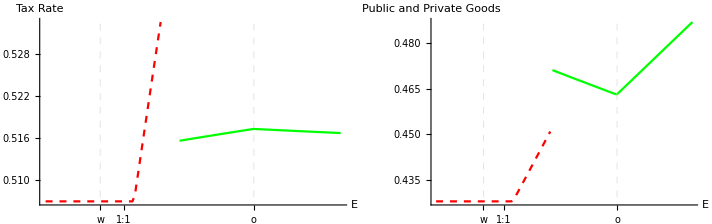

```mathematica
Block[{myParameter="E",
plotLabel="ΔE - Policies: Labor Abundant",
myFilename,
strategies=StrategiesForDeltaProdLabAb,
Players={{3,"Leader"}},
Functions={{getR,"Tax Rate"},{getG,"Public and Private Goods"}},
myTicks={{{100000,"1:1"}},{}},
myPS={{Green},{Dashed,Red}}
},
myFilename="~/_Plots/"<>plotLabel<>".pdf";
Block[{p,player,f,function,idstring,graphic,funcPlotDir,plotfilename,graphics={}},
For[p=1,p≤Length[Players],p++,
player = Players[[p]];
For[f=1,f≤Length[Functions],f++,
function=Functions[[f]];
If[ListQ[function⟦1⟧],function={function⟦1,player⟦1⟧⟧,function⟦2⟧}];
If[function == Null,Continue[]];
graphic=GetPlotGraphic[myParameter,strategies,function,player,""];
AppendTo[graphics,graphic];

(*Export[plotfilename,graphic,myFormat,ImageResolution->300]*);
(*Print[plotfilename];*)
];
graphic=GraphicsGrid[{graphics},PlotLabel->plotLabel,Spacings->-10];
Print[graphic];
Export[myFilename,graphic,"PDF",ImageResolution->300]
]]]
```

#### ΔE - Policies: Capital Abundant

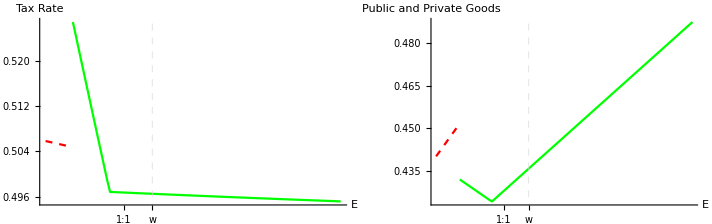

```mathematica
Block[{myParameter="E",
plotLabel="ΔE - Policies: Capital Abundant",
myFilename,
strategies=StrategiesForDeltaProdCapAb,
Players={{3,"Leader"}},
Functions={{getR,"Tax Rate"},{getG,"Public and Private Goods"}},
myTicks={{{100000,"1:1"}},{}},
myPS={{Green},{Dashed,Red}}
},
myFilename="~/_Plots/"<>plotLabel<>".pdf";
Block[{p,player,f,function,idstring,graphic,funcPlotDir,plotfilename,graphics={}},
For[p=1,p≤Length[Players],p++,
player = Players[[p]];
For[f=1,f≤Length[Functions],f++,
function=Functions[[f]];
If[ListQ[function⟦1⟧],function={function⟦1,player⟦1⟧⟧,function⟦2⟧}];
If[function == Null,Continue[]];
graphic=GetPlotGraphic[myParameter,strategies,function,player,""];
AppendTo[graphics,graphic];
];
graphic=GraphicsGrid[{graphics},PlotLabel->plotLabel,Spacings->-10];
Print[graphic];
Export[myFilename,graphic,"PDF",ImageResolution->300]
]]]
```

#### ΔE - Policies: Capital Abundant DOTP and Labor Abundant Plutocracy

```mathematica
Block[{myParameter="E",
plotLabel="ΔE - Policies: Capital Abundant DOTP and Labor Abundant Plutocracy",
myFilename,
strategiesCapAb=StrategiesForDeltaProdCapAb,
strategiesLabAb=StrategiesForDeltaProdLabAb,
Players={{3,"Leader"},{1,"DotP"},{2,"Plutocracy"}},
Functions={{getR,"Tax Rate"}},
myTicks={{{100000,"1:1"}},{}},
myPS={{Green},{Dashed,Red}}
},
myFilename="~/_Plots/"<>plotLabel<>".pdf";
Block[{p,player,f,function,idstring,graphic,funcPlotDir,plotfilename,graphics={}},
For[p=1,p≤Length[Players],p++,
player = Players[[p]];
For[f=1,f≤Length[Functions],f++,
function=Functions[[f]];
If[ListQ[function⟦1⟧],function={function⟦1,player⟦1⟧⟧,function⟦2⟧}];
If[function == Null,Continue[]];
graphic=GraphicsGrid[{{GetPlotGraphic[myParameter,strategiesCapAb,function,player,""]}},PlotLabel->"\nTax rate of DotP as E varies\nin Capital Abundant Country"];
AppendTo[graphics,graphic];
];
];
For[p=1,p≤Length[Players],p++,
player = Players[[p]];
For[f=1,f≤Length[Functions],f++,
function=Functions[[f]];
If[ListQ[function⟦1⟧],function={function⟦1,player⟦1⟧⟧,function⟦2⟧}];
If[function == Null,Continue[]];
graphic=GraphicsGrid[{{GetPlotGraphic[myParameter,strategiesLabAb,function,player,""]}},PlotLabel->"\nTax rate of Plutocracy as E varies\nin Labor Abundant Country"];
AppendTo[graphics,graphic];
];
];

graphic=GraphicsGrid[{{graphics⟦2⟧,graphics⟦6⟧}},PlotLabel->plotLabel,Spacings->-10];
Print[graphic];
Export[myFilename,graphic,"PDF",ImageResolution->300]
]
]
```

-Graphics-

~/_Plots/ΔE - Policies: Capital Abundant DOTP and Labor Abundant Plutocracy.pdf

#### ΔE - Individual Utilities in W

```mathematica
Block[{myParameter="E",
plotLabel="ΔE - Individual Utilities in W",
myFilename,
strategiesCapAb=StrategiesForDeltaProdCapAb,
strategiesLabAb=StrategiesForDeltaProdLabAb,
Players={{3,"Leader"}},
Functions={{getUw,"Worker Utility"},{getUo,"Owner Utility"}},
myTicks={{{100000,"1:1"}},{}},
myPS={{Green},{Dashed,Red}}
},
myFilename="~/_Plots/"<>plotLabel<>".pdf";
Block[{p,player,f,function,idstring,graphic,funcPlotDir,plotfilename,graphics={}},
For[p=1,p≤Length[Players],p++,
player = Players[[p]];
For[f=1,f≤Length[Functions],f++,
function=Functions[[f]];
If[ListQ[function⟦1⟧],function={function⟦1,player⟦1⟧⟧,function⟦2⟧}];
If[function == Null,Continue[]];
graphic=GraphicsGrid[{{GetPlotGraphic[myParameter,strategiesCapAb,function,player,""]}},PlotLabel->"\n(Capital Abundant)"];
AppendTo[graphics,graphic];
];
];
For[p=1,p≤Length[Players],p++,
player = Players[[p]];
For[f=1,f≤Length[Functions],f++,
function=Functions[[f]];
If[ListQ[function⟦1⟧],function={function⟦1,player⟦1⟧⟧,function⟦2⟧}];
If[function == Null,Continue[]];
graphic=GraphicsGrid[{{GetPlotGraphic[myParameter,strategiesLabAb,function,player,""]}},PlotLabel->"\n(Labor Abundant)"];
AppendTo[graphics,graphic];
];
];

graphic=GraphicsGrid[{{graphics⟦4⟧,graphics⟦3⟧},{graphics⟦2⟧,graphics⟦1⟧}},PlotLabel->plotLabel,Spacings->-10];
Print[graphic];
Export[myFilename,graphic,"PDF",ImageResolution->300]
]
]
```

-Graphics-

~/_Plots/ΔE - Individual Utilities in W.pdf

#### ΔE - Individual Values in W

```mathematica
Block[{myParameter="E",
plotLabel="ΔE - Individual Values in W",
myFilename,
strategiesCapAb=StrategiesForDeltaProdCapAb,
strategiesLabAb=StrategiesForDeltaProdLabAb,
Players={{3,"Leader"}},
Functions={{getVw,"Worker Value"},{getVo,"Owner Value"}},
myTicks={{{100000,"1:1"}},{}},
myPS={{Green},{Dashed,Red}}
},
myFilename="~/_Plots/"<>plotLabel<>".pdf";
Block[{p,player,f,function,idstring,graphic,funcPlotDir,plotfilename,graphics={}},
For[p=1,p≤Length[Players],p++,
player = Players[[p]];
For[f=1,f≤Length[Functions],f++,
function=Functions[[f]];
If[ListQ[function⟦1⟧],function={function⟦1,player⟦1⟧⟧,function⟦2⟧}];
If[function == Null,Continue[]];
graphic=GraphicsGrid[{{GetPlotGraphic[myParameter,strategiesCapAb,function,player,""]}},PlotLabel->"\n(Capital Abundant)"];
AppendTo[graphics,graphic];
];
];
For[p=1,p≤Length[Players],p++,
player = Players[[p]];
For[f=1,f≤Length[Functions],f++,
function=Functions[[f]];
If[ListQ[function⟦1⟧],function={function⟦1,player⟦1⟧⟧,function⟦2⟧}];
If[function == Null,Continue[]];
graphic=GraphicsGrid[{{GetPlotGraphic[myParameter,strategiesLabAb,function,player,""]}},PlotLabel->"\n(Labor Abundant)"];
AppendTo[graphics,graphic];
];
];

graphic=GraphicsGrid[{{graphics⟦4⟧,graphics⟦3⟧},{graphics⟦2⟧,graphics⟦1⟧}},PlotLabel->plotLabel,Spacings->-10];
Print[graphic];
Export[myFilename,graphic,"PDF",ImageResolution->300]
]
]
```

-Graphics-

~/_Plots/ΔE - Individual Values in W.pdf

#### ΔE - Economic Inequality

```mathematica
Block[{myParameter="E",
plotLabel="ΔE - Economic Inequality",
myFilename,
strategiesCapAb=StrategiesForDeltaProdCapAb,
strategiesLabAb=StrategiesForDeltaProdLabAb,
Players={{3,"Leader"}},
Functions={{getUoMinusUw, "U(o in W) - U(t in W)"}},
myTicks={{{100000,"1:1"}},{}},
myPS={{Green},{Dashed,Red}}
},
myFilename="~/_Plots/"<>plotLabel<>".pdf";
Block[{p,player,f,function,idstring,graphic,funcPlotDir,plotfilename,graphics={}},
For[p=1,p≤Length[Players],p++,
player = Players[[p]];
For[f=1,f≤Length[Functions],f++,
function=Functions[[f]];
If[ListQ[function⟦1⟧],function={function⟦1,player⟦1⟧⟧,function⟦2⟧}];
If[function == Null,Continue[]];
graphic=GraphicsGrid[{{GetPlotGraphic[myParameter,strategiesCapAb,function,player,""]}},PlotLabel->"\nCapital Abundant"];
AppendTo[graphics,graphic];
];
];
For[p=1,p≤Length[Players],p++,
player = Players[[p]];
For[f=1,f≤Length[Functions],f++,
function=Functions[[f]];
If[ListQ[function⟦1⟧],function={function⟦1,player⟦1⟧⟧,function⟦2⟧}];
If[function == Null,Continue[]];
graphic=GraphicsGrid[{{GetPlotGraphic[myParameter,strategiesLabAb,function,player,""]}},PlotLabel->"\nLabor Abundant"];
AppendTo[graphics,graphic];
];
];

graphic=GraphicsGrid[{{graphics⟦1⟧,graphics⟦2⟧}},PlotLabel->plotLabel,Spacings->-10];
Print[graphic];
Export[myFilename,graphic,"PDF",ImageResolution->300]
]
]
```

-Graphics-

~/_Plots/ΔE - Economic Inequality.pdf

#### ΔE - Inequalities in Plutocracy and DotP

```mathematica
Block[{myParameter="E",
plotLabel="ΔE - Inequalities in Plutocracy and DotP",
myFilename,
strategiesCapAb=StrategiesForDeltaProdCapAb,
strategiesLabAb=StrategiesForDeltaProdLabAb,
Players={{3,"Leader"},{1,"DotP"},{2,"Plutocracy"}},
Functions={{getUoMinusUw, "U(o in W) - U(t in W)"}},
myTicks={{{100000,"1:1"}},{}},
myPS={{Green},{Dashed,Red}}
},
myFilename="~/_Plots/"<>plotLabel<>".pdf";
Block[{p,player,f,function,idstring,graphic,funcPlotDir,plotfilename,graphics={}},
For[p=1,p≤Length[Players],p++,
player = Players[[p]];
For[f=1,f≤Length[Functions],f++,
function=Functions[[f]];
If[ListQ[function⟦1⟧],function={function⟦1,player⟦1⟧⟧,function⟦2⟧}];
If[function == Null,Continue[]];
graphic=GraphicsGrid[{{GetPlotGraphic[myParameter,strategiesCapAb,function,player,""]}},PlotLabel->"\n(Capital Abundant - "<>player⟦2⟧<>")"];
AppendTo[graphics,graphic];
];
];
For[p=1,p≤Length[Players],p++,
player = Players[[p]];
For[f=1,f≤Length[Functions],f++,
function=Functions[[f]];
If[ListQ[function⟦1⟧],function={function⟦1,player⟦1⟧⟧,function⟦2⟧}];
If[function == Null,Continue[]];
graphic=GraphicsGrid[{{GetPlotGraphic[myParameter,strategiesLabAb,function,player,""]}},PlotLabel->"\n(Labor Abundant - "<>player⟦2⟧<>")"];
AppendTo[graphics,graphic];
];
];

graphic=GraphicsGrid[{{graphics⟦2⟧,graphics⟦5⟧},{graphics⟦3⟧,graphics⟦6⟧}},PlotLabel->plotLabel,Spacings->-10];
Print[graphic];
Export[myFilename,graphic,"PDF",ImageResolution->300]
]
]
```

-Graphics-

~/_Plots/ΔE - Inequalities in Plutocracy and DotP.pdf

#### ΔWC - Policies

```mathematica
Block[{myParameter="W",
plotLabel="ΔW - Policies",
myFilename,
strategiesCapAb=StrategiesForDeltaWCCapAb,
strategiesLabAb=StrategiesForDeltaWCLabAb,
Players={{3,"Leader"}},
Functions={{getR,"Tax Rate"},
{getG,"Private Goods"},
{getX,"Public Goods"}},
myTicks={{{.1,"10%"},{.2,"20%"},{.3,"30%"},{.4,"40%"},{.5,"50%"},{.9,"90%"}},{}},
myPS={{Green},{Dashed,Red}}
},
myFilename="~/_Plots/"<>plotLabel<>".pdf";
Block[{p,player,f,function,idstring,graphic,funcPlotDir,plotfilename,graphics={}},
For[p=1,p≤Length[Players],p++,
player = Players[[p]];
For[f=1,f≤Length[Functions],f++,
function=Functions[[f]];
If[ListQ[function⟦1⟧],function={function⟦1,player⟦1⟧⟧,function⟦2⟧}];
If[function == Null,Continue[]];
graphic=GraphicsGrid[{{GetPlotGraphic[myParameter,strategiesCapAb,function,player,""]}},PlotLabel->"\n(Capital Abundant)"];
AppendTo[graphics,graphic];
];
];
For[p=1,p≤Length[Players],p++,
player = Players[[p]];
For[f=1,f≤Length[Functions],f++,
function=Functions[[f]];
If[ListQ[function⟦1⟧],function={function⟦1,player⟦1⟧⟧,function⟦2⟧}];
If[function == Null,Continue[]];
graphic=GraphicsGrid[{{GetPlotGraphic[myParameter,strategiesLabAb,function,player,""]}},PlotLabel->"\n(Labor Abundant)"];
AppendTo[graphics,graphic];
];
];
graphic=GraphicsGrid[{{graphics⟦5⟧,graphics⟦6⟧,graphics⟦4⟧},{graphics⟦2⟧,graphics⟦3⟧,graphics⟦1⟧}},PlotLabel->plotLabel,Spacings->-10];
Print[graphic];
Pause[1];
Export[myFilename,graphic,"PDF",ImageResolution->300]
]
]
```

-Graphics-

~/_Plots/ΔW - Policies.pdf

#### ΔWCw - Policies

```mathematica
Block[{myParameter="W_t",
plotLabel="ΔW_t - Policies",
myFilename,
strategiesCapAb=StrategiesForDeltaWCwCapAb,
strategiesLabAb=StrategiesForDeltaWCwLabAb,
Players={{3,"Leader"}},
Functions={{getR,"Tax Rate"},
{getG,"Private Goods"},
{getX,"Public Goods"}},
myTicks={{{.1,"10%"},{.25,"25%"},{.5,"50%"},{.9,"90%"}},{}},
myPS={{Green},{Dashed,Red}}
},
myFilename="~/_Plots/"<>plotLabel<>".pdf";
Block[{p,player,f,function,idstring,graphic,funcPlotDir,plotfilename,graphics={}},
For[p=1,p≤Length[Players],p++,
player = Players[[p]];
For[f=1,f≤Length[Functions],f++,
function=Functions[[f]];
If[ListQ[function⟦1⟧],function={function⟦1,player⟦1⟧⟧,function⟦2⟧}];
If[function == Null,Continue[]];
graphic=GraphicsGrid[{{GetPlotGraphic[myParameter,strategiesCapAb,function,player,""]}},PlotLabel->"\n(Capital Abundant)"];
AppendTo[graphics,graphic];
];
];
For[p=1,p≤Length[Players],p++,
player = Players[[p]];
For[f=1,f≤Length[Functions],f++,
function=Functions[[f]];
If[ListQ[function⟦1⟧],function={function⟦1,player⟦1⟧⟧,function⟦2⟧}];
If[function == Null,Continue[]];
graphic=GraphicsGrid[{{GetPlotGraphic[myParameter,strategiesLabAb,function,player,""]}},PlotLabel->"\n(Labor Abundant)"];
AppendTo[graphics,graphic];
];
];

graphic=GraphicsGrid[{{graphics⟦5⟧,graphics⟦6⟧,graphics⟦4⟧},{graphics⟦2⟧,graphics⟦3⟧,graphics⟦1⟧}},PlotLabel->plotLabel,Spacings->-10];
Print[graphic];
Export[myFilename,graphic,"PDF",ImageResolution->300]
]
]
```

-Graphics-

~/_Plots/ΔW_t - Policies.pdf

#### ΔWCo - Policies

```mathematica
Block[{myParameter="W_o",
plotLabel="ΔW_o - Policies",
myFilename,
strategiesCapAb=StrategiesForDeltaWCoCapAb,
strategiesLabAb=StrategiesForDeltaWCoLabAb,
Players={{3,"Leader"}},
Functions={{getR,"Tax Rate"},
{getG,"Private Goods"},
{getX,"Public Goods"}},
myTicks={{{.1,"10%"},{.25,"25%"},{.5,"50%"},{.9,"90%"}},{}},
myPS={{Green},{Dashed,Red}}
},
myFilename="~/_Plots/"<>plotLabel<>".pdf";
Block[{p,player,f,function,idstring,graphic,funcPlotDir,plotfilename,graphics={}},
For[p=1,p≤Length[Players],p++,
player = Players[[p]];
For[f=1,f≤Length[Functions],f++,
function=Functions[[f]];
If[ListQ[function⟦1⟧],function={function⟦1,player⟦1⟧⟧,function⟦2⟧}];
If[function == Null,Continue[]];
graphic=GraphicsGrid[{{GetPlotGraphic[myParameter,strategiesCapAb,function,player,""]}},PlotLabel->"\n(Capital Abundant)"];
AppendTo[graphics,graphic];
];
];
For[p=1,p≤Length[Players],p++,
player = Players[[p]];
For[f=1,f≤Length[Functions],f++,
function=Functions[[f]];
If[ListQ[function⟦1⟧],function={function⟦1,player⟦1⟧⟧,function⟦2⟧}];
If[function == Null,Continue[]];
graphic=GraphicsGrid[{{GetPlotGraphic[myParameter,strategiesLabAb,function,player,""]}},PlotLabel->"\n(Labor Abundant)"];
AppendTo[graphics,graphic];
];
];

graphic=GraphicsGrid[{{graphics⟦5⟧,graphics⟦6⟧,graphics⟦4⟧},{graphics⟦2⟧,graphics⟦3⟧,graphics⟦1⟧}},PlotLabel->plotLabel,Spacings->-10];
Print[graphic];
Export[myFilename,graphic,"PDF",ImageResolution->300]
]
]
```

-Graphics-

~/_Plots/ΔW_o - Policies.pdf

#### ΔWC* - Values and Inequalities

```mathematica
Block[{myParameter="WCo",
plotLabel="ΔW - Values and Inequalities",
myFilename,
strategiesCapAb=StrategiesForDeltaWCCapAb,
strategiesLabAb=StrategiesForDeltaWCLabAb,
strategiesCapAbw=StrategiesForDeltaWCwCapAb,
strategiesLabAbw=StrategiesForDeltaWCwLabAb,
strategiesCapAbo=StrategiesForDeltaWCoCapAb,
strategiesLabAbo=StrategiesForDeltaWCoLabAb,
Players={{3,"Leader"}},
Functions={{getVw,"Worker Value"},{getVo,"Owner Value"},{getUoMinusUw, "U(o in W) - U(t in W)"}},
myTicks={{{.1,"10%"},{.25,"25%"},{.5,"50%"},{.9,"90%"}},{}},
myPS={{Green},{Dashed,Red}}
},
myFilename="~/_Plots/"<>plotLabel<>".pdf";
Block[{p,player,f,function,idstring,graphic,funcPlotDir,plotfilename,graphics={}},
For[p=1,p≤Length[Players],p++,
player = Players[[p]];
For[f=1,f≤Length[Functions],f++,
function=Functions[[f]];
If[ListQ[function⟦1⟧],function={function⟦1,player⟦1⟧⟧,function⟦2⟧}];
If[function == Null,Continue[]];
graphic=GraphicsGrid[{{GetPlotGraphic["W",strategiesCapAb,function,player,""]}},PlotLabel->"\n(ΔW - Capital Abundant)"];
AppendTo[graphics,graphic];
];
];
For[p=1,p≤Length[Players],p++,
player = Players[[p]];
For[f=1,f≤Length[Functions],f++,
function=Functions[[f]];
If[ListQ[function⟦1⟧],function={function⟦1,player⟦1⟧⟧,function⟦2⟧}];
If[function == Null,Continue[]];
graphic=GraphicsGrid[{{GetPlotGraphic["W",strategiesLabAb,function,player,""]}},PlotLabel->"\n(ΔW - Labor Abundant)"];
AppendTo[graphics,graphic];
];
];
For[p=1,p≤Length[Players],p++,
player = Players[[p]];
For[f=1,f≤Length[Functions],f++,
function=Functions[[f]];
If[ListQ[function⟦1⟧],function={function⟦1,player⟦1⟧⟧,function⟦2⟧}];
If[function == Null,Continue[]];
graphic=GraphicsGrid[{{GetPlotGraphic["W_t",strategiesCapAbw,function,player,""]}},PlotLabel->"\n(ΔW_t - Capital Abundant)"];
AppendTo[graphics,graphic];
];
];
For[p=1,p≤Length[Players],p++,
player = Players[[p]];
For[f=1,f≤Length[Functions],f++,
function=Functions[[f]];
If[ListQ[function⟦1⟧],function={function⟦1,player⟦1⟧⟧,function⟦2⟧}];
If[function == Null,Continue[]];
graphic=GraphicsGrid[{{GetPlotGraphic["W_t",strategiesLabAbw,function,player,""]}},PlotLabel->"\n(ΔW_t - Labor Abundant)"];
AppendTo[graphics,graphic];
];
];
For[p=1,p≤Length[Players],p++,
player = Players[[p]];
For[f=1,f≤Length[Functions],f++,
function=Functions[[f]];
If[ListQ[function⟦1⟧],function={function⟦1,player⟦1⟧⟧,function⟦2⟧}];
If[function == Null,Continue[]];
graphic=GraphicsGrid[{{GetPlotGraphic["W_o",strategiesCapAbo,function,player,""]}},PlotLabel->"\n(ΔW_o - Capital Abundant)"];
AppendTo[graphics,graphic];
];
];
For[p=1,p≤Length[Players],p++,
player = Players[[p]];
For[f=1,f≤Length[Functions],f++,
function=Functions[[f]];
If[ListQ[function⟦1⟧],function={function⟦1,player⟦1⟧⟧,function⟦2⟧}];
If[function == Null,Continue[]];
graphic=GraphicsGrid[{{GetPlotGraphic["W_o",strategiesLabAbo,function,player,""]}},PlotLabel->"\n(ΔW_o - Labor Abundant)"];
AppendTo[graphics,graphic];
];
];

graphic=GraphicsGrid[{{graphics⟦2⟧,graphics⟦13⟧,graphics⟦8⟧},{graphics⟦3⟧,graphics⟦18⟧,graphics⟦12⟧}},PlotLabel->plotLabel,Spacings->-10];
Print[graphic];
Export[myFilename,graphic,"PDF",ImageResolution->300]
]
]
```

-Graphics-

~/_Plots/ΔW - Values and Inequalities.pdf

#### ΔWC* - Utilities and Inequalities

```mathematica
Block[{myParameter="WC*",
plotLabel="ΔW - Utilities and Inequalities",
myFilename,
strategiesCapAb=StrategiesForDeltaWCCapAb,
strategiesLabAb=StrategiesForDeltaWCLabAb,
strategiesCapAbw=StrategiesForDeltaWCwCapAb,
strategiesLabAbw=StrategiesForDeltaWCwLabAb,
strategiesCapAbo=StrategiesForDeltaWCoCapAb,
strategiesLabAbo=StrategiesForDeltaWCoLabAb,
Players={{3,"Leader"}},
Functions={{getUw,"Worker Utility"},{getUo,"Owner Utility"},{getUoMinusUw, "U(o in W) - U(t in W)"}},
myTicks={{{.1,"10%"},{.25,"25%"},{.5,"50%"},{.9,"90%"}},{}},
myPS={{Green},{Dashed,Red}}
},
myFilename="~/_Plots/"<>plotLabel<>".pdf";
Block[{p,player,f,function,idstring,graphic,funcPlotDir,plotfilename,graphics={}},
For[p=1,p≤Length[Players],p++,
player = Players[[p]];
For[f=1,f≤Length[Functions],f++,
function=Functions[[f]];
If[ListQ[function⟦1⟧],function={function⟦1,player⟦1⟧⟧,function⟦2⟧}];
If[function == Null,Continue[]];
graphic=GraphicsGrid[{{GetPlotGraphic["W",strategiesCapAb,function,player,""]}},PlotLabel->"\n(ΔW - Capital Abundant)"];
AppendTo[graphics,graphic];
];
];
For[p=1,p≤Length[Players],p++,
player = Players[[p]];
For[f=1,f≤Length[Functions],f++,
function=Functions[[f]];
If[ListQ[function⟦1⟧],function={function⟦1,player⟦1⟧⟧,function⟦2⟧}];
If[function == Null,Continue[]];
graphic=GraphicsGrid[{{GetPlotGraphic["W",strategiesLabAb,function,player,""]}},PlotLabel->"\n(ΔW - Labor Abundant)"];
AppendTo[graphics,graphic];
];
];
For[p=1,p≤Length[Players],p++,
player = Players[[p]];
For[f=1,f≤Length[Functions],f++,
function=Functions[[f]];
If[ListQ[function⟦1⟧],function={function⟦1,player⟦1⟧⟧,function⟦2⟧}];
If[function == Null,Continue[]];
graphic=GraphicsGrid[{{GetPlotGraphic["W_t",strategiesCapAbw,function,player,""]}},PlotLabel->"\n(ΔW_t - Capital Abundant)"];
AppendTo[graphics,graphic];
];
];
For[p=1,p≤Length[Players],p++,
player = Players[[p]];
For[f=1,f≤Length[Functions],f++,
function=Functions[[f]];
If[ListQ[function⟦1⟧],function={function⟦1,player⟦1⟧⟧,function⟦2⟧}];
If[function == Null,Continue[]];
graphic=GraphicsGrid[{{GetPlotGraphic["W_t",strategiesLabAbw,function,player,""]}},PlotLabel->"\n(ΔW_t - Labor Abundant)"];
AppendTo[graphics,graphic];
];
];
For[p=1,p≤Length[Players],p++,
player = Players[[p]];
For[f=1,f≤Length[Functions],f++,
function=Functions[[f]];
If[ListQ[function⟦1⟧],function={function⟦1,player⟦1⟧⟧,function⟦2⟧}];
If[function == Null,Continue[]];
graphic=GraphicsGrid[{{GetPlotGraphic["W_o",strategiesCapAbo,function,player,""]}},PlotLabel->"\n(ΔW_o - Capital Abundant)"];
AppendTo[graphics,graphic];
];
];
For[p=1,p≤Length[Players],p++,
player = Players[[p]];
For[f=1,f≤Length[Functions],f++,
function=Functions[[f]];
If[ListQ[function⟦1⟧],function={function⟦1,player⟦1⟧⟧,function⟦2⟧}];
If[function == Null,Continue[]];
graphic=GraphicsGrid[{{GetPlotGraphic["W_o",strategiesLabAbo,function,player,""]}},PlotLabel->"\n(ΔW_o - Labor Abundant)"];
AppendTo[graphics,graphic];
];
];

graphic=GraphicsGrid[{{graphics⟦2⟧,graphics⟦14⟧,graphics⟦8⟧},{graphics⟦1⟧,graphics⟦13⟧,graphics⟦7⟧},{graphics⟦3⟧,graphics⟦9⟧,graphics⟦15⟧}},PlotLabel->plotLabel,Spacings->-10];
Print[graphic];
Export[myFilename,graphic,"PDF",ImageResolution->300]
]
]
```

-Graphics-

~/_Plots/ΔW - Utilities and Inequalities.pdf

#### Open-close lines as Co/Cw varies

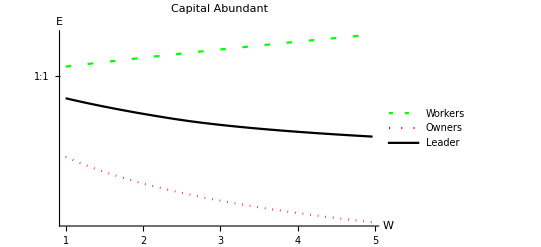

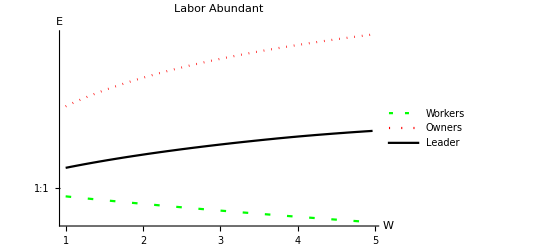

```mathematica
g  = PlotOpeningOfBorders[DeltaCoOverCwBordersCapitalAbundant, "Capital Abundant"];
Export["~/_Plots/DeltaCoOverCwBordersCapitalAbundant.pdf",g,"PDF",ImageResolution->300];
Print[g];
g  = PlotOpeningOfBorders[DeltaCoOverCwBordersLaborAbundant, "Labor Abundant"];
Export["~/_Plots/DeltaCoOverCwBordersLaborAbundant.pdf",g,"PDF",ImageResolution->300];
Print[g];
```